```mathematica
SetDirectory[NotebookDirectory[]];
t1 = Import["oned.h5", {"Datasets", "/1/t"}];
space1 = Import["oned.h5", {"Datasets", "/1/space"}];
meandensity1 = Import["oned.h5", {"Datasets", "/1/mean_density"}];
stderrdensity1 = Import["oned.h5", {"Datasets", "/1/stderr_density"}];
ResetDirectory[];
SetDirectory[NotebookDirectory[]];
t2 = Import["oned.h5", {"Datasets", "/2/t"}];
meanpescape2 = Import["oned.h5", {"Datasets", "/2/mean_pescape"}];
stderrpescape2 = Import["oned.h5", {"Datasets", "/2/stderr_pescape"}];
ResetDirectory[];
SetDirectory[NotebookDirectory[]];
t3 = Import["oned.h5", {"Datasets", "/3/t"}];
meanNtot3 = Import["oned.h5", {"Datasets", "/3/mean_Ntot"}];
stderrNtot3 = Import["oned.h5", {"Datasets", "/3/stderr_Ntot"}];
ResetDirectory[];

declaredVariables={"t1", "space1", "meandensity1", "stderrdensity1", "t2", "meanpescape2", "stderrpescape2", "t3", "meanNtot3", "stderrNtot3"}
```

{t1,space1,meandensity1,stderrdensity1,t2,meanpescape2,stderrpescape2,t3,meanNtot3,stderrNtot3}

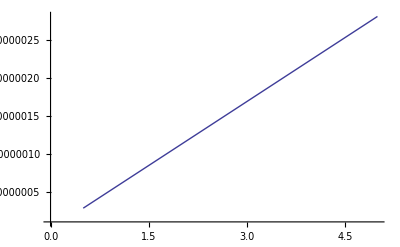

```mathematica
ListLinePlot[Transpose[{t3,meanNtot3}]]
```

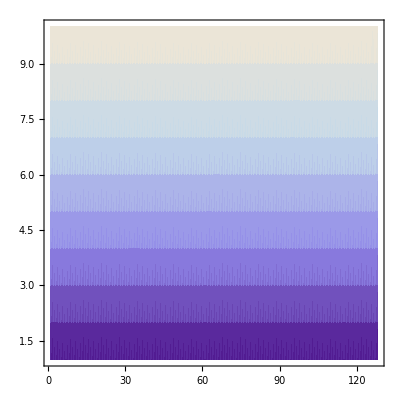

```mathematica
ListDensityPlot[meandensity1]
```

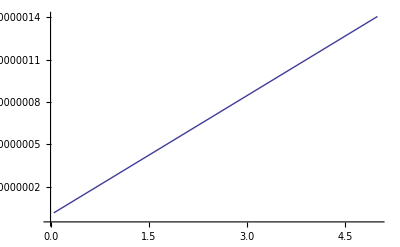

```mathematica
ListLinePlot[Transpose[{t2,meanpescape2}]]
```

```mathematica
meanpescape2
```

{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}